# Project report

## Chromatography of SANS 342 diesel.

D Malan

Department of Chemistry
University of Pretoria

23 December 2019

## Introduction

The FAMEs content of biodiesel is described by SANS 1935, and the PAH content and FAMEs content of diesel fuels by SANS 342. There is considerable overlap between the two methods (Thesis, Fig 3.5).

{-Graphics-}

Using SFC we cover FAMEs (GC), C18:3, iodine value, and PUFA for biodiesel. We can include glycerol and glycerides if we add methanol modifier to the SFC mobile phase. 
But we can also do PAHs using SFC (Thesis, Fig 6.7).
FAMEs interfere with the official method for PAHs in diesel. ASTM D6591 (Standard Test Method for Determination of Aromatic Hydrocarbon Types in Middle Distillates—High Performance Liquid Chromatography Method with Refractive Index Detection). ASTM D5186 (the SFC method) also claims that biodiesel will interfere. The alternative to these methods is ASTM D2425, a mass spectrometry method.
SANS 342 offers an IR method for determining FAMEs, based on the carbonyl stretch band. This method is subject to interferences from oxidation products.

Using SFC×GC for biodiesel blends can give us all the information we need to determine PAHs and FAMEs in diesel, which may contain up to 5% of FAMEs. No interferences are expected.

I discovered an SOP by the California Air Resources Board that analyses PAHs in diesel by SFC, then backflushes the FAMEs off the column to determine total FAMEs. If all the compounds are allowed to elute, then we can do SFC×GC and get much more information. 

Alternative methods: http://fuelregulations.com/astm-methods/

## Experimental

### Details

Here we give some detail about the experimental results

### Standards available

```mathematica
pahlist = {"Anthracene", "Chrysene", "Fluoranthene","BenzoApyrene", "BenzoGhiPerylene","Fluorene","Acenaphthylene", "Indeno1,2,3CdPyrene"}
```

{Anthracene,Chrysene,Fluoranthene,BenzoApyrene,BenzoGhiPerylene,Fluorene,Acenaphthylene,Indeno1,2,3CdPyrene}

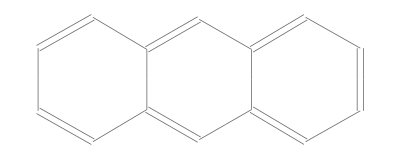
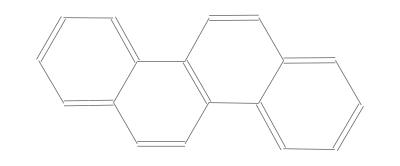
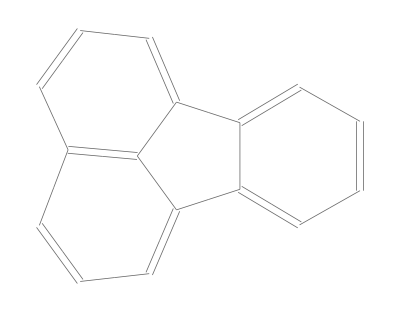
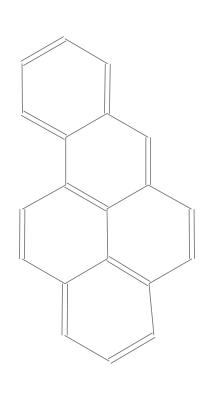
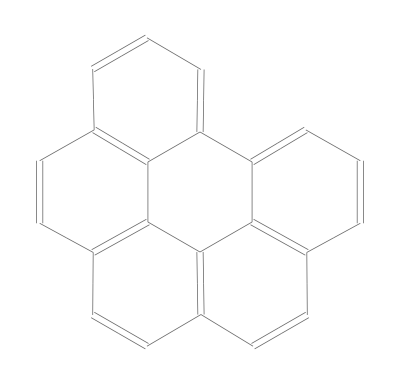
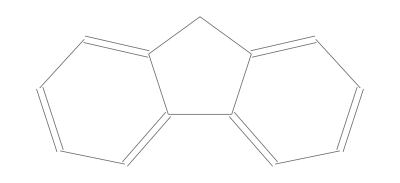
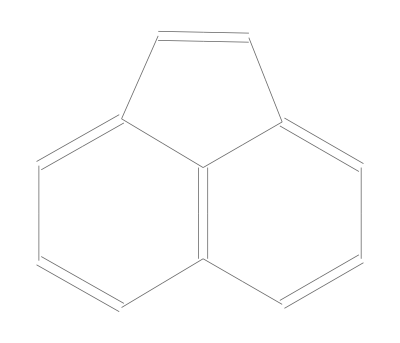
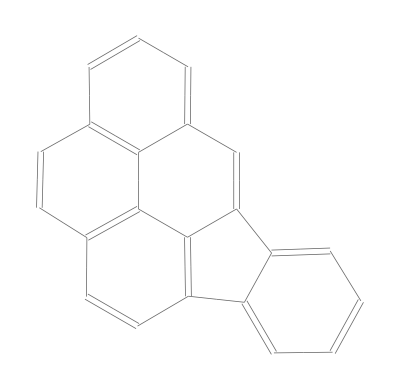
anthracene | -Graphics-
chrysene | -Graphics-
fluoranthene | -Graphics-
benzo[a]pyrene | -Graphics-
1,12-benzoperylene | -Graphics-
fluorene | -Graphics-
acenaphthylene | -Graphics-
indeno[1,2,3-cd]pyrene | -Graphics-

```mathematica
{ChemicalData[#, "Name"],ChemicalData[#]}&/@ pahlist//TableForm
```

```mathematica
lipidlist = {"Trilaurin", "Trimyristin", "Tripalmitin", "Tristearin", "Dilaurin", "Dimyristin", "Dipalmitin", "Distearin" }
```

{Trilaurin,Trimyristin,Tripalmitin,Tristearin,Dilaurin,Dimyristin,Dipalmitin,Distearin}

```mathematica
TableForm[lipidlist]
```

Trilaurin
Trimyristin
Tripalmitin
Tristearin
Dilaurin
Dimyristin
Dipalmitin
Distearin

I also have available the samples of Elize Smit, together with a summary of their contents. This will make a very good comparison.

## Calculations

```mathematica
ChemicalData["BenzoApyrene", "BoilingPoint"]
```

495. °C

## Results

## Discussion

## Conclusion

## Recommendations